```mathematica
messageHandler=If[Last[#],Abort[]]&
Internal`AddHandler["Message",messageHandler]
```

If[Last[#1],Abort[]]&

```mathematica
Internal`RemoveHandler["Message",messageHandler]
```

## Read in results (delete!)

```mathematica
homdirectory=ParentDirectory[NotebookDirectory[]]; (*set home directory here*)
wd=StringJoin[homdirectory,"/Smn1/"];
SetDirectory[wd];
figpath=StringJoin[homdirectory, "/figures"];
```

```mathematica
alpha=4;(* alleles per site *)
l=8;(* length of sequence *)
A=Range[0,alpha-1];(*the alphabet in numbers 0-3*)
sequences=Tuples[A,l];(*list of all sequences*)
sequences9=Tuples[{A,A,A,{2},A,A,A,A,A}];(*list of all length 9 sequences with +1 fixed to be G*)
nfaces=Binomial[l,2] ((alpha(alpha-1))^2 ) alpha^(l-2); (*number of 2-faces*)
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];(*multiplicites of eigenvalues lambda_k, k=0,1,...,l*)
wt="CAGUAAGU";
wt9nt="CAGGUAAGU";
AA={"A","C","G","U"};
AAtoDigitRules = {"A"->0,"C"->1,"G"->2,"U"->3};(*convert nucleotides to numbers*)
AAtoDigitRulesQ={"'A'"->0,"'C'"->1,"'G'"->2,"'U'"->3};
DigitToAARules = {0->"A",1->"C",2->"G",3->"U"};(*convert numbers to nucleotides*)
sequences9AA=StringJoin[#/.DigitToAARules]&/@sequences9;
```

```mathematica
Data=Rest[Import["data/psi_9nt.txt","TSV"]];
```

```mathematica
list={"-3","-2","-1","+2","+3","+4","+5","+6"};
```

```mathematica
seq2pos[seq_]:=FromDigits[seq,alpha]+1;(*maps a sequence tuple to its lexicographical order*)
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules](*maps a sequence string to its lexicographical order*)
```

```mathematica
seqlistAll=Range[alpha^l];
seqlistUC=seq2pos/@Tuples[{A,A,A,{1,3},A,A,A,A}];
seqlistAG=seq2pos/@Tuples[{A,A,A,{0,2},A,A,A,A}];
seqlistNGU=seq2pos/@Tuples[{A,{2},{3},A,A,A,A,A}];
```

```mathematica
proportions=Join[{.05},Range[0.1,.9,.1],{.93}];
samplesizes=Ceiling[.5alpha^l proportions];
nrep=5;
```

```mathematica
trs=Import["data/trsrep.m"];
tts=Table[Complement[seqlistSmn1,trs[[i,j]]],{i,Length@proportions},{j,nrep}];
pdsVC =Import["out/pdsVCrep.m"];
pdsGE=Import[ "out/pdsGErep.m"];
pds1way=Import[ "out/pds1way.m"];
pds2wayEN=Import[ "out/pds2wayEN.m"];
pds3wayEN=Import[ "out/pds3wayEN.m"];
```

```mathematica
VarLT={112.25340685502368,74.00070816938819,97.66491016207033,73.44470047871346,95.48570589509103,90.82741238612005,85.57024307709577,75.38415343910737,73.38807694768923,57.16789171568365,82.02988591711835,88.33416236320659,86.51885951040128,87.37788668463634,72.40240003630169,55.59595768783703,68.04793497931433,56.98303378469831,72.41115707575136,89.54801409845896,98.0512962468984,92.75708579625899,67.66869713040904,75.18861346403082,79.09362278010838,102.84506135482138,79.97427622855929,90.99836039894745,90.8425459022584,92.01683545631761,79.7771705800252,74.02264854544023,84.54993839408866,62.90870190678328,78.29824963241163,80.54226819823845,75.6424941722106,94.5173504595731,81.60359686101197,101.9923074310712};
```

## Preparation

```mathematica
(*set 0^0=1*)
Unprotect[Power];
Power[0|0.,0|0.]=1;
Protect[Power];
```

```mathematica
homdirectory=ParentDirectory[NotebookDirectory[]]; (*set home directory here*)
wd=StringJoin[homdirectory,"/Smn1/"];
SetDirectory[wd];
figpath=StringJoin[homdirectory, "/figures"];
```

```mathematica
(*create folders*)
Quiet[CreateDirectory[{FileNameJoin[{wd,#}]}]
,CreateDirectory::filex
]&/@{"../figures","output_python","GE","out"};
```

### parameters

```mathematica
alpha=4;(* alleles per site *)
l=8;(* length of sequence *)
A=Range[0,alpha-1];(*the alphabet in numbers 0-3*)
sequences=Tuples[A,l];(*list of all sequences*)
sequences9=Tuples[{A,A,A,{2},A,A,A,A,A}];(*list of all length 9 sequences with +1 fixed to be G*)
nfaces=Binomial[l,2] ((alpha(alpha-1))^2 ) alpha^(l-2); (*number of 2-faces*)
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];(*multiplicites of eigenvalues lambda_k, k=0,1,...,l*)
wt="CAGUAAGU";
wt9nt="CAGGUAAGU";
AA={"A","C","G","U"};
AAtoDigitRules = {"A"->0,"C"->1,"G"->2,"U"->3};(*convert nucleotides to numbers*)
AAtoDigitRulesQ={"'A'"->0,"'C'"->1,"'G'"->2,"'U'"->3};
DigitToAARules = {0->"A",1->"C",2->"G",3->"U"};(*convert numbers to nucleotides*)
sequences9AA=StringJoin[#/.DigitToAARules]&/@sequences9;
```

```mathematica
Data=Rest[Import["data/psi_9nt.txt","TSV"]];
```

```mathematica
list={"-3","-2","-1","+2","+3","+4","+5","+6"};
```

```mathematica
seq2pos[seq_]:=FromDigits[seq,alpha]+1;(*maps a sequence tuple to its lexicographical order*)
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules](*maps a sequence string to its lexicographical order*)
```

```mathematica
seqlistAll=Range[alpha^l];
seqlistUC=seq2pos/@Tuples[{A,A,A,{1,3},A,A,A,A}];
seqlistAG=seq2pos/@Tuples[{A,A,A,{0,2},A,A,A,A}];
seqlistNGU=seq2pos/@Tuples[{A,{2},{3},A,A,A,A,A}];
```

### Functions

#### basic functions

```mathematica
greekletter[l_]:=Style[l/.{Alpha->α, Beta->β, Gamma->γ, Rho->ρ, Lambda ->λ},FontFamily->"Stencil", FontSize->16]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
r2[x_,y_]:=Correlation[x,y]^2;
mse[x_,y_]:=Mean[(x-y)^2];
maxorder[list_]:=Module[{i},For[i=1,list[[i;;]]!=ConstantArray[0,Length[list[[i;;]]]],i++];i-1];
```

```mathematica
w[k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q] (*Krawtchouk polynomial*)
wkd = Table[w[k,d],{d,0,l},{k,0,l}]; (*Krawtchouk matrix*)
```

```mathematica
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]
```

#### Data Functions

```mathematica
truncate[fit_]:=If[fit<0,0,If[fit>100,100,fit]]
```

```mathematica
nNA[vec_]:=Total[Boole/@NumberQ/@vec]
```

```mathematica
nRep[vec_]:=Total[Boole/@NumberQ/@vec]
```

```mathematica
nZeros[vec_]:=Length[Select[vec,#==0&]]
```

```mathematica
median[vec_]:=Module[{vec2},
vec2=Select[vec,NumberQ];
If[Length@vec2==0,"NaN",Median@vec2]
]
```

```mathematica
mean[vec_]:=Module[{vec2},
vec2=Select[vec,NumberQ];
If[Length@vec2==0,"NaN",Mean@vec2]
]
```

```mathematica
log[x_]:=If[NumberQ[x]==True,If[x==0,"NaN",Log[x]],"NaN"]
```

```mathematica
std[vec_]:=Module[{vec2},
vec2=Select[vec,NumberQ];
If[Length@vec2<2,"NaN",StandardDeviation@vec2]
]
```

```mathematica
toPSI[vec_]:=(100/vec[[posWT]]) vec
```

```mathematica
BCGM[vec_]:=Exp[Mean[Log/@vec]-Variance[Log/@vec]/(2Length[vec])]
```

```mathematica
BCGM2[vec_]:=Exp[Mean[Log/@vec]-Delta^2/(2Length[vec])]
```

```mathematica
BCStd[vec_]:=Module[{n,sig2,mustar},
n=Length@vec;
sig2=Variance[Log/@vec];
mustar=Mean[Log/@vec]-sig2/(2 n);Sqrt[(Exp[sig2/n]-1) Exp[2 mustar+sig2/n]]]
```

```mathematica
BCStd2[vec_]:=Module[{mustar,n},
n=Length[vec];
mustar=Mean[Log/@vec]-Delta^2/(2 n);Sqrt[(Exp[Delta^2/n]-1) Exp[2 mustar+Delta^2/n]]]
```

```mathematica
BCStd0[vec_]:=Module[{mustar,n},
n=Length[vec];
mustar=Log[Median[vec]/.{0.->0}];
Sqrt[(Exp[Delta^2/n]-1) Exp[2 mustar+Delta^2/n]]]
```

```mathematica
BCStdAll[vec_]:=
If[nZeros[vec]==0,
If[
Length[vec]==1,
BCStd0[vec],
BCStd[vec]
],
BCStd0[vec]]
```

```mathematica
seq2pos9AA[seq_]:=seq2pos[Characters[seq][[{1,2,3,5,6,7,8,9}]]/.AAtoDigitRules]
```

```mathematica
maketips[coords_,labels_]:=Table[{Black,PointSize[.02],Tooltip[Point[coords[[i]]],labels[[i]]]},{i,Length@labels}]
```

```mathematica
hd1nbs[seq_]:=Flatten[Table[Table[ReplacePart[seq,{i->j}],{j,Complement[A,{seq[[i]]}]}],{i,Length[seq]}],1]
```

```mathematica
printfasta[seqs_]:=CopyToClipboard[ExportString[{Range[Length[seqs]],seqs},"FASTA"]]
```

#### regressions

```mathematica
s2dTaylor[seq_,order_,wt_]:=Module[{seqprime,sub1,sub2,pos},
seqprime=Mod[seq-wt,alpha];
sub1=Subsets[seqprime,{order}];
sub2=Table[Join[{i},sub1[[i]]],{i,Length[sub1]}];pos=FromDigits[Rest[#]-1,alpha-1]+1+(#[[1]]-1)*((alpha-1)^order)&/@Select[sub2,!MemberQ[#,0]&];
SparseArray[Table[pos[[i]]->1,{i,Length[pos]}],{Binomial[l,order]*(alpha-1)^order}]
]
```

```mathematica
s2d[seq_,order_]:=Module[{sub1,sub2,pos},
sub1=Subsets[seq,{order}];
sub2=Table[Join[{i},sub1[[i]]],{i,Length[sub1]}];pos=FromDigits[Rest[#],alpha]+1+(#[[1]]-1)*(alpha^order)&/@sub2;
SparseArray[Table[pos[[i]]->1,{i,Length[pos]}],{Binomial[l,order]*(alpha)^order}]
]
```

```mathematica
null=Table[Join[s2dTaylor[sequences[[i]],0,Characters[wt]/.AAtoDigitRules],s2dTaylor[sequences[[i]],1,Characters[wt]/.AAtoDigitRules]],{i,Length[sequences]}];//AbsoluteTiming
```

{6.52519,Null}

```mathematica
OrdinaryRegression[design_,response_]:=Module[{cross},
cross=Transpose[design].design;
LinearSolve[cross,Transpose[design].response]]
```

#### Global epistasis

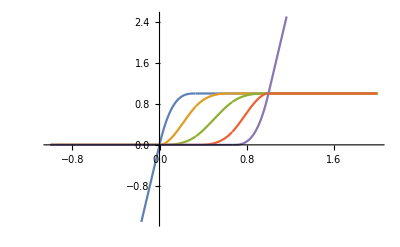

```mathematica
deg=2; (*M-spline basis degree, I-spline degree is deg+1*)
elem=5; (*Number of splines in finished basis*)
knots=Range[0,1,1/(elem-deg)];
knots=Join[ConstantArray[knots[[1]],deg],knots,ConstantArray[knots[[-1]],deg]];
Table[Integrate[BSplineBasis[{deg,knots},i,x],x],{i,0,Length[knots]-deg-2}];
ReplacePart[%,
{{1,1,1,1}->BSplineBasis[{deg,knots},0,0]x,{-1,1}->Join[%[[-1,1]] ,{{(%[[-1]]/.x->1)+BSplineBasis[{deg,knots},Length[knots]-deg-2,1](x-1),x>1}}]}];
(basis=%/%[[All,2]]//Simplify);
Plot[Evaluate[basis],{x,-1,2}]
```

```mathematica
transform[phi_,a_]:=First[a]+basis.Rest[a]/.{x->phi}
```

#### plotting

```mathematica
labelfigs[figs_]:=Table[
Labeled[figs[[i]],Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica",FontSize->fontsize],{{Top,Left}}],
{i,Length[figs]}
]
```

```mathematica
ScatterPlot[pd_,true_,plotlab_]:=Show[ListPlot[Transpose@{pd,true},BaseStyle->{FontSize->16},PlotStyle->{{GrayLevel[.2],PointSize[.01]}},PlotRange->{{-20,200},{-20,200}},AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Range[0,200,50],False},{Range[0,200,50],False}},FrameLabel->None,PlotLabel->Style[plotlab,Black,FontSize->16],FrameStyle->fstyle],Plot[x,{x,-100,200},PlotStyle->GrayLevel[.8]],
Graphics[Inset[Column[{Style[Style[Subscript[Superscript[R,2],"test"],Italic]==Round[r2[pd,true],.01],GrayLevel[.2],FontSize->16], Style[Style[Subscript[RMSE,"test"],Italic]==Round[Sqrt@mse[pd,true],.1],GrayLevel[.2],FontSize->16]},Alignment->Left],{130,20}]],ImageSize->300]
```

```mathematica
ScatterPlot2[pd_,true_,plotlab_, xlab_, ylab_]:=Show[ListPlot[Transpose@{pd,true},BaseStyle->{FontSize->16},PlotStyle->{{GrayLevel[.2],PointSize[.01]}},PlotRange->{{-20,200},{-20,200}},AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Range[0,200,50],False},{Range[0,200,50],False}},FrameLabel->{xlab,ylab},PlotLabel->Style[plotlab,Black,FontSize->16],FrameStyle->fstyle],Plot[x,{x,-100,200},PlotStyle->GrayLevel[.8]],
Graphics[Inset[Column[{Style[Style[Subscript[Superscript[R,2],"test"],Italic]==Round[r2[pd,true],.01],GrayLevel[.2],FontSize->16], Style[Style[Subscript[RMSE,"test"],Italic]==Round[Sqrt@mse[pd,true],.1],GrayLevel[.2],FontSize->16]},Alignment->Left],{130,20}]],ImageSize->300]
```

#### Variance component functions

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
MakeAdj[A_,l_]:=SparseArray[
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]
```

```mathematica
Adj=MakeAdj[alpha,l];//AbsoluteTiming
```

{9.77294,Null}

```mathematica
MakeLaplacian[A_,l_]:=SparseArray[
Join[Table[{i,i}->l(A-1),{i,1,A^l}],
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]
L=MakeLaplacian[alpha,l];//AbsoluteTiming
```

{10.3776,Null}

```mathematica
MakeLapRec[alpha_,l_]:=Module[{L1,L,m},
L1 = SparseArray[alpha*IdentityMatrix[alpha] - ArrayReshape[ConstantArray[1,alpha^2],{alpha,alpha}]];
m=1;
L=L1;
While[m<l, L = KroneckerProduct[L, IdentityMatrix[alpha]] + KroneckerProduct[IdentityMatrix[alpha^m],L1];
m++];
L
]
```

```mathematica
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1]
```

```mathematica
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;
```

```mathematica
degree=(alpha-1)*l;
```

```mathematica
nbsizes=Table[Binomial[l,p](alpha-1)^p,{p,0,l}]
```

{1,24,252,1512,5670,13608,20412,17496,6561}

```mathematica
CollapsedAdjEntries[d1_,d2_]:=(1/((alpha-1)*l))If[Abs[d1-d2]>1,0,If[d1==d2,d1(alpha-2),If[d1>d2,(l-d2)(alpha-1),d2]]];
```

```mathematica
NCAdj=Table[CollapsedAdjEntries[d1,d2],{d1,0,l},{d2,0,l}];
```

```mathematica
phisd=NestList[NCAdj.#&,PadRight[{1},l+1],l];
```

```mathematica
AnEntries=Table[degree^s*(phisd[[s+1]]/nbsizes),{s,0,l}];
```

```mathematica
RdCoeffsAn=Table[LinearSolve[Transpose@AnEntries,ReplacePart[ConstantArray[0,l+1],{i->1}]],{i,l+1}];
```

```mathematica
EAC[y_,list_]:=Module[{PresenceAbsence,npairsd,AB},
AB=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{alpha^l,Length[list]}];
PresenceAbsence=AB.ConstantArray[1,Length[list]];
npairsd=Table[PresenceAbsence.(RdCoeffsAn[[i]].NestList[Adj.#&,PresenceAbsence,l]),{i,l+1}];
Table[((AB.y).(RdCoeffsAn[[i]].NestList[Adj.#&,AB.y,l]))/npairsd[[i]],{i,l+1}]]
```

```mathematica
LambdaLS[list_,y_,var_]:=Module[{m,Ab,PresenceAbsence,npairsd,rowmeans,Mmatrix,rhod,a,v,lambdaest,CinLn},
Mmatrix=Table[0,l+1,l+1];
m=Length@list;
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{alpha^l,Length[list]}];
PresenceAbsence=Ab.ConstantArray[1,Length[list]];
npairsd=Table[PresenceAbsence.(RdCoeffsAn[[k]].NestList[Adj.#&,PresenceAbsence,l]),{k,l+1}];
Do[
Mmatrix[[i,j]]=Mmatrix[[j,i]]=npairsd.(wkd[[All,i]]*wkd[[All,j]]),{i,1,l+1},
{j,1,i}
];
rhod=EAC[y,list]-PadRight[{Mean[var]},l+1];
a=Table[npairsd.(wkd[[All,i]]*rhod),{i,l+1}];
v=Array[p,l+1];
lambdaest=(Last@NMinimize[{v.Mmatrix.v-2v.a+(rhod^2).npairsd,v>0},v,Method->{"Automatic"},MaxIterations->10000])[[All,2]];
{rhod,lambdaest}
]
```

```mathematica
GPinterpol[lambdas_,list_,y_,var_]:=Module[
{KerninLn,KbbBy,Alph,Ab,Ai},
Ab=SparseArray[Transpose[{list,Range[Length[list]]}]->1,{alpha^l,Length[list]}];
Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],list],Range[alpha^l-Length[list]]}]->1,{alpha^l,alpha^l-Length[list]}];
KerninLn=Inverse[LPs].(wkd[[All,All]].lambdas);
KbbBy[vec_]:=(Transpose[Ab].SprsinLnBy[Ab.vec,KerninLn]+MakeDiagonal[var].vec);
Alph=LinearSolve[KbbBy[#]&,y,Method->{"Krylov",Method->"ConjugateGradient",MaxIterations->10000}];
SprsinLnBy[Ab.Alph,KerninLn]
]
```

```mathematica
VCLS[list_,y_,var_]:=Module[{lambdas},
lambdas=LambdaLS[list,y,var][[2]];
{lambdas,GPinterpol[lambdas,list,y,var]}
]
```

## Process library data

```mathematica
ratiosrep=Import["data/ratios_9nt_ss_rep.txt","TSV"];
```

```mathematica
missing=Flatten@Position[nRep/@ratiosrep[[2;;,-7;;]],0];
Length@missing
```

2036

```mathematica
Smn1Rep=(Transpose@Join[{ratiosrep[[2;;,1]]},Transpose@ratiosrep[[2;;,-7;;]]]);
Smn1Rep=Smn1Rep[[Complement[Range@Length[Smn1Rep],missing]]];
posWT=First@Flatten@Position[Smn1Rep[[All,1]],"CAGGUAAGU"];
seqs=Smn1Rep[[All,1]];
Smn1Rep=Select[#,NumberQ]&/@Smn1Rep;
Smn1Rep=Smn1Rep/.{0.->0};
```

```mathematica
Smn1RepA=(Transpose@Join[{ratiosrep[[2;;,1]]},Transpose@ratiosrep[[2;;,-7;;]]]);
Smn1RepA=Smn1RepA[[Complement[Range@Length[Smn1RepA],missing]]];
```

```mathematica
Smn1Nreps=Transpose@{seqs,Length/@(Select[#,NumberQ]&/@Smn1RepA[[All,2;;]])};
```

```mathematica
Smn1RepLog=Smn1Rep;
Do[Smn1RepLog[[i]]=log/@Smn1Rep[[i]],{i,Length@Smn1RepLog}];
```

```mathematica
Smn1RepLog=Select[#,NumberQ]&/@Smn1RepLog;
```

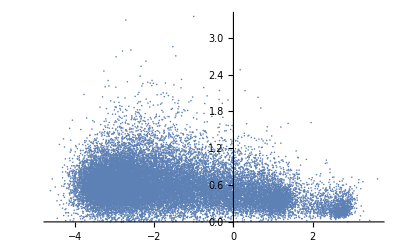

```mathematica
Smn1Log=Transpose@{seqs,mean/@Smn1RepLog[[All]],std/@Smn1RepLog[[All]],nRep/@Smn1RepLog[[All]]};
ListPlot[Transpose@{Smn1Log[[All,2]],Smn1Log[[All,3]]},PlotRange->All]
```

```mathematica
posNZ=Flatten@Position[nZeros/@Smn1Rep,0];
posAZ=Flatten@Position[nZeros[#]==Length[#]&/@Smn1Rep,True];
pos1Rep=Flatten@Position[nRep/@Smn1Rep,1];
posReps=Table[Flatten@Position[nRep/@Smn1Rep,rep],{rep,7}];
```

```mathematica
Delta=Smn1Log[[Complement[posNZ,pos1Rep],3]]//Median
```

0.480621

```mathematica
FactorPSI=100/BCGM[Smn1Rep[[posWT]]];
```

```mathematica
Smn1Med=Table[0,Length[Smn1Rep]];
Do[Smn1Med[[i]]=BCGM[Smn1Rep[[i]]],{i,Complement[posNZ,pos1Rep]}];
Do[Smn1Med[[i]]=Median[Smn1Rep[[i]]],{i,Complement[Range[Length@Smn1Rep],Complement[posNZ,pos1Rep]]}];
Smn1Med=toPSI[ Smn1Med];
```

```mathematica
Smn1Std=FactorPSI BCStdAll/@Smn1Rep;
StdMin=Quantile[Smn1Std,.2];
Smn1Std=If[#>StdMin,#,StdMin]&/@Smn1Std;
```

```mathematica
Smn1Data=Transpose@{Smn1RepA[[All,1]],Smn1Med,Smn1Std,ConstantArray["Smn1",Length[Smn1Med]]};
```

```mathematica
seqlistSmn1=seq2pos[Characters[#][[Complement[Range[9],{4}]]]/.AAtoDigitRules]&/@Smn1Data[[All,1]];
```

```mathematica
responseSmn1=MapPartialVal[seqlistSmn1,Smn1Data[[All,2]],alpha^l];
```

```mathematica
variance = Smn1Std^2;
varall = MapPartialVal[seqlistSmn1,variance, alpha^l];
```

```mathematica
missing >> "data/Smn1MissingList.m"
Smn1Data >> "data/Smn1Data.m"
seqlistSmn1 >> "data/seqlistSmn1.m"
```

### Export to Python

```mathematica
Export["data/seqsSmn1.txt",sequences[[seqlistSmn1]] ,"CSV"];
Export["data/seqlist.txt",seqlistSmn1,"CSV"];
Export["data/var.txt",varall,"CSV"];
Export["data/response.txt",responseSmn1,"CSV"];
```

## Python prep

Export data to Python for later analyses

import os
os.chdir("/Users/keitokiddo/VC")
import scipy as sp
import sys
sys.path.insert(1, '/Users/keitokiddo/git/vcregression/vcregression')

import vc_regression as vc
import itertools
import os
import csv
import pandas as pd
import numpy as np
import arrow
import scipy as sp

#define sequence space parameters
alpha, l = 4, 8 #alpha: alphabet size; l: sequence length
G = alpha**l
bases = np.array(range(alpha))
seqs = list(itertools.product(bases, repeat=l)) #generate all possible sequences

#prepare python
vc.preliminary_preparation(alpha, l)
dirin = "Smn1/data/"
dirout = "Smn1/output_python/"

#read in data
seqlist=pd.read_csv(dirin + "seqlist.txt", sep=',',header=None).T
seqlist=seqlist.values.tolist()[0]
seqlist=[seqlist[i] - 1 for i in range(len(seqlist))]

response=pd.read_csv(dirin + "response.txt", sep=',',header=None).T
response=response.values.tolist()[0]
response=np.array(response)

varall=pd.read_csv(dirin + "var.txt", sep=',',header=None).T
varall=varall.values.tolist()[0]

vc.sample_name = "smn1"

Loading L_sparse ...

0.06 sec

# define function to map between sequence representations
alphabet = {"A","C","G","U"}

AA2N = dict([(sorted(alphabet)[i], i) for i in range(len(alphabet))])
N2AA = {v: k for k, v in AA2N.items()}
AA = list(AA2N.keys())
seqsAll = [''.join(seq) for seq in itertools.product(AA, repeat=l)]
vc.seqsAll = seqsAll


def seqAA2num(seq):
    return [AA2N[seq[i]] for i in range(len(seq))]

ExternalFunction[…]

## Comparing performance with other models

### Training data sampling

```mathematica
proportions=Join[{.05},Range[0.1,.9,.1],{.93}];
samplesizes=Ceiling[.5alpha^l proportions];
nrep=5;
```

```mathematica
trs=Table[RandomSample[seqlistSmn1,i],{i,samplesizes},nrep];
```

```mathematica
Export["trsrep.m",trs];
```

```mathematica
Do[Export[StringJoin["data/tr_",ToString[i],"_",ToString[j],".tsv"],trs[[i,j]],"TSV"],{i,Length@samplesizes},{j,nrep}]
```

### Additive

```mathematica
pds1way=Table[null.OrdinaryRegression[null[[trs[[i,j]]]],responseSmn1[[trs[[i,j]]]]],{i,Length[trs]},{j,nrep}];
```

### GE

```mathematica
SetDirectory[StringJoin[wd,"/GE"]];
```

#### Export data to Julia

```mathematica
Do[Export[StringJoin["Smn1","_",ToString[i],"_",ToString[j],".txt"],Prepend[Smn1Data[[Flatten[Position[seqlistSmn1,#]&/@trs[[i,j]]]]],{"mut","f","v","condition"}],"CSV"],{i,Length[trs]},{j,nrep}]
```

#### Compile command lines in Julia

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin["Smn1","_",ToString[i],"_",ToString[j],".txt"]],"d = prepdata(dataf, :mut, :sequence, \"CAGGUAAGU\", :f, cname = :condition, vname = :v)","@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[ToString[i],"_",ToString[j]]]},{i,Length[trs]},{j,nrep}];
```

```mathematica
Export["terminal.txt",Join[{StringReplace["cd(\"#comparison/GE\")","#"->wd],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

#### Copy and execute commands in “terminal.txt” in Julia

#### read in Julia outputs

```mathematica
pdsGErep=Table[{},Length[trs],nrep];
```

```mathematica
Do[pdsGErep[[i,j]]=Module[{y,b,a,yhat,spline,PossibleEffects,FactorMatrix,SortedEffects,Effects,coeffsAll},
b=Transpose[Import[StringReplace["b_#.tsv","#"->StringJoin[ToString[i],"_",ToString[j]]]]]//Flatten;
a=Transpose[Import[StringReplace["a_#.tsv","#"->StringJoin[ToString[i],"_",ToString[j]]]]]//Flatten;
yhat=Transpose[Import[StringReplace["yhat_#.tsv","#"->StringJoin[ToString[i],"_",ToString[j]]]]]//Flatten;
spline[x_]:=transform[x,a];
PossibleEffects=Complement[Join[Tuples[{Range[8],AA}],{{"Smn1"}}],Thread[{Range[8],Characters[wt]}]];FactorMatrix=Table[Join[{Smn1Data[[k,4]]},Thread[{Range[8],Characters[Smn1Data[[k,1]]][[{1,2,3,5,6,7,8,9}]]}]],{k,Flatten[Position[seqlistSmn1,#]&/@trs[[i,j]]]}];SortedEffects=SortBy[Transpose[{PossibleEffects,Table[Min[Position[Flatten[FactorMatrix,1],PossibleEffects[[i]]]],{i,Length[PossibleEffects]}]}],Last];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];coeffsAll=MapPartialVal[(FromDigits[#,4]&/@(Effects[[1;;22]]/.AAtoDigitRules/.Table[list[[i]]->i,{i,Length[list]}])) -4+1,b[[2;;23]],32];spline/@Table[s2d[sequences[[i]],1].coeffsAll+b[[1]],{i,alpha^l}]
],{i,Length[trs]},{j,nrep}]
```

```mathematica
pdsGErep>> "out/pdsGErep.m";
```

```mathematica
SetDirectory[StringJoin[wd]];
```

### Elastic net

```mathematica
SetDirectory[wd];
```

#### Export design matrix

```mathematica
designrulesonehot[seq_, order_,j_]:=Module[{ sub1, sub2, pos},
  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] , alpha ] + 
      1 + (#[[1]]-1 )*((alpha )^order)+ Total@Table[Binomial[l,k](alpha)^(k),{k,0,order-1}]& /@ 
    sub2;
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2donehot[seqs_,order_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrulesonehot[seqs[[j]],k,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha ^k),{k,order}]}]]
```

```mathematica
rules=Flatten[Table[Join[Table[designrulesonehot[sequences[[j]],k,j],{k,8}]],{j,Length[sequences]}],2];//AbsoluteTiming
```

{277.192,Null}

```mathematica
nullonehot=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*(alpha)^k,{k,0,8}]}];
```

```mathematica
Export["glmnet/rules.tsv",Transpose@{Most[ArrayRules[nullonehot]][[All,1]][[All,1]],Most[ArrayRules[nullonehot]][[All,1]][[All,2]]},"TSV"];
```

#### Run “glmnet/Smn1.R” file in R

#### Read in glmnet results

```mathematica
modelname="3way_EN";
pds3wayEN=Table[{},Length[samplesizes],nrep];
Do[pds3wayEN[[i,j]]=Flatten@Import[StringJoin["glmnet/pd_",modelname,"_",ToString[i],"_",ToString[j],".tsv"],"TSV"][[2;;,2;;]],{i,Length[trs]},{j,nrep}];
```

```mathematica
modelname="2way_EN";
pds2wayEN=Table[{},Length[samplesizes],nrep];
Do[pds2wayEN[[i,j]]=Flatten@Import[StringJoin["glmnet/pd_",modelname,"_",ToString[i],"_",ToString[j],".tsv"],"TSV"][[2;;,2;;]],{i,Length[trs]},{j,nrep}];
```

### VC

for i in range(11):
    for j in range(5):
        print("working on sample " + str(i+1) + "," + str(j+1))
        tr = pd.read_csv(dirin + "tr_" + str(i+1) + "_" + str(j+1) + ".tsv", header = None)
        tr = np.array(tr).flatten()
        tr -= 1
        lambdas,map = vc.compute_posterior_mean_ex(np.array(seqs)[tr], np.array(response)[tr], np.array(varall)[tr])
        pd.DataFrame(map).to_csv(dirout + "/map_" + str(i+1) + "_" + str(j+1) + ".tsv", header = None, index = None)
        pd.DataFrame(lambdas).to_csv(dirout + "/lda_" + str(i+1) + "_" + str(j+1) + ".tsv", header = None, index = None)

#### Import python outputs

```mathematica
pdsVC = Table[{},18,3];
```

```mathematica
Do[pdsVC[[i,j]] = Import[StringJoin["output_python/map_", ToString[i], "_", ToString[j], ".tsv"]]//Flatten,{i,11},{j,3}];
```

### Comparison with ME interpolation

```mathematica
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2]
Cinterp[training_,y_]:=Module[
{Ai,Ab},
Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];
Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient",Tolerance->10^-15}])+Ab.y]
```

```mathematica
pdsME=Table[Cinterp[trs[[i,j]],responseSmn1[[trs[[i,j]]]]],{i,11},{j,5}];//AbsoluteTiming
```

{45.6033,Null}

```mathematica
r2sME=Table[r2[pdsME[[i,j]][[Complement[seqlistSmn1,trs[[i,j]]]]],responseSmn1[[Complement[seqlistSmn1,trs[[i,j]]]]]],{i,Length[proportions]},{j,5}];
```

```mathematica
plotdatME=Table[{Around[proportions[[i]],0],Around[Mean[r2sME[[i]]],StandardDeviation[r2sME[[i]]]]},{i,Length[proportions]}]
```

{{0.05,0.3780.015},{0.1,0.5040.016},{0.2,0.6190.004},{0.3,0.6740.005},{0.4,0.7060.008},{0.5,0.7400.006},{0.6,0.7510.007},{0.7,0.7750.005},{0.8,0.7820.012},{0.9,0.7970.022},{0.93,0.8160.033}}

```mathematica
plotdatVC=Table[{Around[proportions[[i]],0],Around[Mean[R2s[[1]][[i]]],StandardDeviation[R2s[[1]][[i]]]]},{i,Length[proportions]}];
```

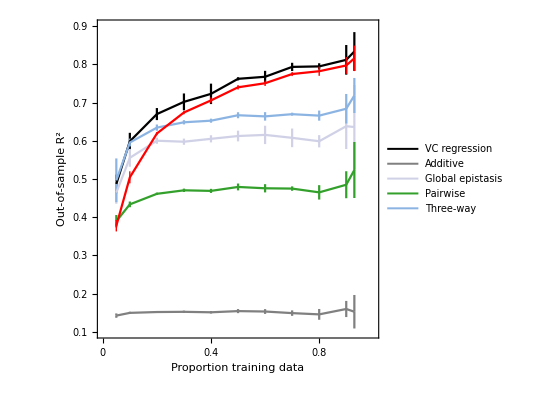

```mathematica
Show[figr2,ListLinePlot[plotdatME,PlotStyle->Red]]
```

```mathematica
fontsize=19;
thickness=AbsoluteThickness[2];
pt=.2;
fstyle=Table[{GrayLevel[.3],AbsoluteThickness[1]},4];
```

```mathematica
style={#,thickness}&/@colors;
```

```mathematica
r2plotMESmn1=ListPlot[
{plotdatVC,plotdatME},
BaseStyle->{FontSize->20},
AspectRatio->1,
PlotRange->{{0,1},{.1,.9}},
Frame->True,
PlotStyle->Join[{{Black,thickness,PointSize[.2]}},{{Red,thickness,PointSize[.2]}}],
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->True,
IntervalMarkersStyle->thickness,
ClippingStyle->None,
ImageSize->400,(*PlotLegends->Placed[LineLegend[Automatic,Join[modellabs[[;;1]],{Style["ME interpolation",FontFamily->"Helvetica"]}],LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}],*) 
PlotLabel->Style["SMN1",Black,FontSize->20]];
```

```mathematica
r2plotMEGB1=Import[FileNameJoin[{figpath,"r2_vc_me_GB1.m"}]];
```

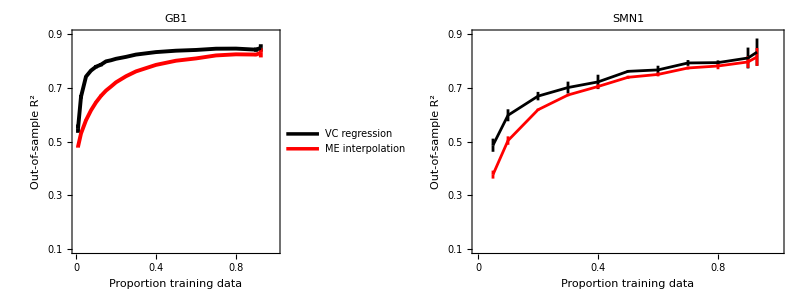

```mathematica
Grid[{{r2plotMEGB1,r2plotMESmn1}},Spacings->2*{1, 1}]
```

```mathematica
Export[FileNameJoin[{figpath,"r2_vc_me.pdf"}],%];
```

#### Scatter plots of predictions

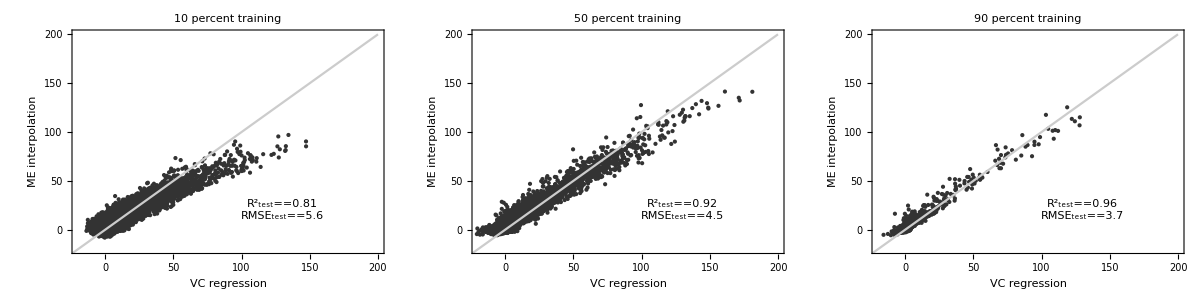

```mathematica
Grid[{Table[ScatterPlot2[pdsVC[[i,j]][[Complement[seqlistSmn1,trs[[i,j]]]]],pdsME[[i,j]][[Complement[seqlistSmn1,trs[[i,j]]]]],Style[StringJoin[ToString[proportions[[i]]*100//IntegerPart]," percent training"],FontFamily->"Helvetica",FontSize->18],Style["VC regression",FontFamily->"Helvetica",FontSize->18],Style["ME interpolation",FontFamily->"Helvetica",FontSize->18]],{i,{2,6,-2}}]}]
```

```mathematica
Export[FileNameJoin[{figpath,"scatter_vc_me_SMN1.pdf"}],%];
```

```mathematica
i=-3;
j=1;
```

```mathematica
ts=Complement[seqlistSmn1,trs[[i,j]]];
```

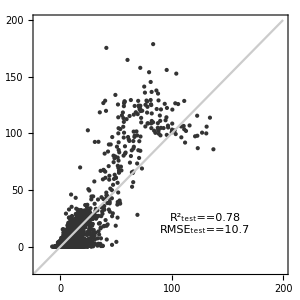

```mathematica
ScatterPlot[pdsME[[i,j]][[ts]],responseSmn1[[ts]],""]
```

## Imputation and posterior sampling for full landscape

### Analysis and imputation of full landscape

lambdas, map = vc.compute_posterior_mean_ex(np.array(seqs)[seqlist], np.array(response)[seqlist], np.array(varall)[seqlist])

pd.DataFrame(map).to_csv(dirout + "/map_all_data" + ".tsv", header = None, index = None)

pd.DataFrame(lambdas).to_csv(dirout + "/lda_all_data" + ".tsv", header = None, index = None)

### Posterior sampling

vc.lda_star = np.array(pd.read_csv(dirout + '/lda_all_data.tsv', header = None)).flatten()
map = np.array(pd.read_csv(dirout + '/map_all_data.tsv', header = None)).flatten()

vc.set_data_as_global_parameters(np.array(seqs)[seqlist], np.array(response)[seqlist], np.array(varall)[seqlist])
vc.prepare_pos_sampling()
vc.outpath = dirout

start_time = arrow.now().format('YYYY-MM-DD-HH-mm')
vc.start_time = start_time

samples = vc.hamiltonian_monte_carlo(
    n_samples = 2000,
    m = 1,
    initial_position = np.zeros(alpha**l),
    tune = 100,
    initial_step_size = 1e-05,
    num_steps = 100,
    max_energy_change=1000.0
  )

currently working on step 1

initial_potential =  0.0

final_potential =  8.10815198276334

energy_change =  3.1683885026723146e-07

p accept =  0.9999996831611999

current step size = 0.0023624295582082688

current acceptance ratio = 1.0

currently working on step 2

initial_potential =  8.10815198276334

final_potential =  6538.857470986998

energy_change =  7.259689007434645

p accept =  0.0007033267309827533

current step size = 0.00010042483077393646

current acceptance ratio = 0.5

currently working on step 3

initial_potential =  8.10815198276334

final_potential =  810.9523067048233

energy_change =  0.00302269977692049

p accept =  0.9969818639806025

current step size = 0.0017696819939808073

current acceptance ratio = 0.6666666666666666

currently working on step 4

initial_potential =  810.9523067048233

final_potential =  7469.292483821724

energy_change =  4.648307380703045

p accept =  0.00957779978701598

current step size = 0.00010411085563608467

current acceptance ratio = 0.5

currently working on step 5

initial_potential =  810.9523067048233

final_potential =  1508.8251726515864

energy_change =  0.0027669717965181917

p accept =  0.9972368527416668

current step size = 0.0014830166738422123

current acceptance ratio = 0.6

currently working on step 6

initial_potential =  1508.8251726515864

final_potential =  5458.404829679956

energy_change =  0.6061806244397303

p accept =  0.5454300982554684

current step size = 0.0017112759767930186

current acceptance ratio = 0.5

currently working on step 7

initial_potential =  1508.8251726515864

final_potential =  6969.923949981883

energy_change =  2.765334507334046

p accept =  0.06295503690388098

current step size = 0.0001758433415433368

current acceptance ratio = 0.42857142857142855

currently working on step 8

initial_potential =  1508.8251726515864

final_potential =  2981.60641715289

energy_change =  0.015566572721581906

p accept =  0.9845539601332784

current step size = 0.001813788764710219

current acceptance ratio = 0.5

currently working on step 9

initial_potential =  2981.60641715289

final_potential =  7792.123232064509

energy_change =  2.496948426560266

p accept =  0.0823358696064357

current step size = 0.00023337235432336736

current acceptance ratio = 0.4444444444444444

currently working on step 10

initial_potential =  2981.60641715289

final_potential =  4564.489711973976

energy_change =  0.026075904388562776

p accept =  0.9742611361062505

current step size = 0.00201040496275716

current acceptance ratio = 0.5

currently working on step 11

initial_potential =  4564.489711973976

final_potential =  8039.961292546013

energy_change =  0.8702688888733974

p accept =  0.4188389129815517

current step size = 0.0012961362671134737

current acceptance ratio = 0.45454545454545453

currently working on step 12

$Aborted

samples0=samples[0]

samples0 = map + samples0
pd.DataFrame(samples0).to_csv(dirout + '/hmc_samples' + '.txt', header = None, index = None)

samples = pd.read_csv(dirout + '/hmc_samples' + '.txt', header = None)
samples = np.array(samples)

bases8 = []
for i in range(8):
  bases8.append(bases)
 
bases8[3] = np.array([1,3])
seqsGU = list(itertools.product(*list(bases8)))
seqlistGU = [vc.seq2pos(seq) for seq in seqsGU]

lambdaspos = []

for i in np.arange(0, 1000, 10):
    rhod,_ = vc.compute_rhod_and_Nd_custom(np.array(samples0)[i][seqlistGU], seqlistGU)
    lambdas = sp.linalg.inv(vc.W_kd.T).dot(rhod)
    lambdaspos.append(lambdas)

pd.DataFrame(lambdaspos).to_csv(dirout + "/posterior_lambdas.csv", header = None, index = None)

## Make Figure 3

### Plotting parameters

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

#### Colors

```mathematica
blue=RGBColor@@({5,112,176}/255);
lightblue=RGBColor@@({116,169,207}/255);
colors={GrayLevel[.7],RGBColor@@({116,196,118}/255),Lighter[lightblue,.2],Darker[blue,.2],Black}//Reverse;
```

#### Sizes

```mathematica
fontsize=19;
thickness=AbsoluteThickness[1.2];
pt=.2;
```

#### Styles

```mathematica
fstyle=Table[{GrayLevel[.3],AbsoluteThickness[1]},4];
```

```mathematica
style={#,thickness}&/@colors;
```

```mathematica
(*barstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.2],"WhiskerStyle"->Black|>;*)
```

```mathematica
barstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.2]|>;
ebstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.3]|>;
(*Bar style - R2 plots*)
R2ErrorBarStyle={#,thickness}&/@colors;
```

```mathematica
(*

R2ErrorBarStyle={#,thickness,AbsolutePointSize[.02]}&/@colors;
(*Bar style - summary plots*)barstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},"FenceWidth"->Scaled[.4],"WhiskerStyle"->Black|>;
(*Frame style*)
*)
```

#### Labels

```mathematica
modelnames={"VC regression","Three-way","Pairwise","Global epistasis","Additive"};
modellabs=Style[#,FontFamily->"Helvetica"]&/@modelnames;
```

### Plotting functions

```mathematica
errorplotdat[data_]:=Module[{means},
means=Mean@data;
Table[Around[means[[i]], {Quantile[data[[All,i]],.025]-means[[i]],Quantile[data[[All,i]],.975]-means[[i]]}],{i,Dimensions[data][[2]]}]
]
```

```mathematica
w[alpha_,l_,k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q] (*Krawtchouk polynomial*)
```

```mathematica
greekletter[l_]:=Style[l/.{Alpha->α, Beta->β, Gamma->γ, Rho->ρ, Lambda ->λ},FontFamily->"Stencil", FontSize->16]
```

```mathematica
summaryfig3[lambdas_,lambdaspos_, vcs_,  alpha_, l_]:=Module[
{},
wkd = Table[w[alpha,l, k,d],{d,0,l},{k,0,l}];
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
(*rho prior*)
rho = wkd[[All,2;;]].Rest[lambdas];
plotdat=Transpose@{Range[0,l],Nbyfirst[rho]};
figrho=Show[
ListLinePlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",ToString[ρ]},
FrameTicks->{{Range[0,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
PlotStyle->{GrayLevel[.5], thickness},
BaseStyle->{FontSize->fontsize},
ImageSize->400,
AspectRatio->.75,
PlotRange->{{0,l+.2},{-.12,1}},
PlotRangeClipping->False
],
ListPlot[
plotdat,
PlotStyle->{Gray}
]
];
(*rho posterior*)
rhopos = Table[Nbyfirst[wkd[[All,2;;]].Rest[lambdaspos[[i]]]],{i,Length[lambdaspos]}];
plotdat=errorplotdat[rhopos];
figrhopos = Show[
ListPlot[
plotdat,DataRange->{0,l},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],
ListLinePlot[Join[{1},plotdat[[2;;,1]]],DataRange->{0,l},PlotRange->All,PlotStyle->{GrayLevel[.25], thickness}]];(*vc prior*)
vc=Transpose@{Range[1,l],Nbysum[Rest@lambdas*Rest@multiplicities]};
figvcBar=BarChart[vc[[All,2]],ChartLabels->vc[[All,1]],
Frame->True,
FrameLabel->{"Interaction order","Variance explained"},
FrameTicks->{{Range[0,1,.1]/.{0.->0},None},{Range[1,l,1],None}},
FrameStyle->fstyle,
BaseStyle->{FontSize->fontsize},
ChartStyle->GrayLevel[.7],
ImageSize->400,
PlotRange->{{.5,l+.5},All},
PlotRangeClipping->False,
AspectRatio->.75
];
(*vc posterior*)
vcpos = Table[Nbysum[Rest@lambdaspos[[i]]*Rest@multiplicities],{i,Length[lambdaspos]}];
plotdat = errorplotdat[vcpos];
figvcpos = Show[
ListPlot[plotdat,DataRange->{1,l},PlotStyle->{GrayLevel[.25],thickness},IntervalMarkersStyle->barstyle,Joined->False],
ListLinePlot[plotdat[[All,1]],DataRange->{1,l},PlotStyle->{GrayLevel[.25],thickness}]];
(*Gamma Prior*)
ck = Table[Table[2^k (-1)^q Binomial[k,q],{q,0,l}],{k,0,l}];
mk=Table[Table[PadLeft[ck[[k]],l+d][[;;l+1]],{d,1,l+1}],{k,l+1}];
gammak=Table[(mk[[k]].wkd.lambdas),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
gammak=Table[(mk[[k]].rho),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
k=1;
figgamma=Table[
Module[{plotdat},
plotdat=Transpose@{Range[0,Length[gammak[[k+1]]]-1],Nbyfirst[gammak[[k+1]]]};
Show[
ListLinePlot[
plotdat,
Frame->True,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],ToString[k]]},
FrameTicks->{{Range[0,2,.2]/.{0.->0,1.->1},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->fontsize},
PlotStyle->{GrayLevel[.5], thickness},
ImageSize->400,
AspectRatio->.75,
FrameStyle->fstyle,
PlotRange->{{0,l+.2},{-.12,1}},
PlotRangeClipping->False],
ListPlot[
plotdat,
PlotStyle->{Gray}]]
],{k,0,3}];
(*Gamma posterior*)
gamma1pos=Table[Most[mk[[2]].rhopos[[i]]],{i,Length[rhopos]}];
gamma1pos = Nbyfirst/@gamma1pos;
plotdat = errorplotdat[gamma1pos];
figgamma1pos = Show[
ListPlot[plotdat,DataRange->{0,l-1},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],
ListLinePlot[Join[{1},plotdat[[2;;,1]]],DataRange->{0,l-1},PlotRange->All,PlotStyle->{GrayLevel[.25], thickness}]];
{Show[figrho,figrhopos],Show[figvcBar,figvcpos],Show[figgamma[[2]],figgamma1pos]}
]
```

```mathematica
MakeR2figure[r2s_]:=Module[
{},
plotdatError=Table[Table[{Around[proportions[[i]],0],Around[Mean[r2s[[k,i]]],StandardDeviation[r2s[[k,i]]]]},{i,Length[proportions]}],{k,Length[r2s]}];
plotdatLine=Table[Table[{proportions[[i]],Mean[r2s[[k,i]]]},{i,Length[proportions]}],{k,Length[r2s]}];
figR2Line=ListPlot[
plotdatLine,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->True,
PlotRangeClipping->False,
ImageSize->400,
AxesOrigin->{0,.8},
AxesStyle->Directive[Transparent,Dashed],PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->16,GrayLevel[.4]},Spacings->.2,LegendMargins->0,LegendMarkerSize->{28,2}],{.75,.3}]];
figR2Error=ListPlot[
plotdatError,
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
IntervalMarkersStyle->R2ErrorBarStyle,
PlotStyle->style,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->False,
PlotRangeClipping->False,
ImageSize->400];
Show[figR2Line,figR2Error]
]
```

```mathematica
labelfigs[figs_]:=Table[
Show[figs[[i]], Epilog->Text[Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica", FontSize->fontsize+2],ImageScaled@{0.02,.95}],ImagePadding->{{65,5},{60,10}}],
{i,Length[figs]}
]
```

```mathematica
labelfigs[fig_,lab_]:=Show[fig, Epilog->Text[Style[lab,Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{.04,.95}],ImagePadding->{{80,5},{60,20}}]
```

```mathematica
labelfigspad[fig_,lab_,pad_]:=Show[fig, Epilog->Text[Style[lab,Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{.04,.95}],ImagePadding->pad]
```

### Import posterior statistics

#### MAP

```mathematica
map = Import["output_python/map_all_data.tsv"]//Flatten;
```

#### Prior lambdas

```mathematica
lambdaest = Import["output_python/lda_all_data.tsv", "CSV"]//Flatten;
rho = wkd[[All,2;;]].Rest[lambdaest];
```

#### Posterior lambdas

```mathematica
lambdaspos = Import["output_python/posterior_lambdas.csv"];
```

### Plotting

```mathematica
vc=Transpose@{Range[1,l],Nbysum[Rest@lambdaest*Rest@multiplicities]};
```

```mathematica
pdsAll={pdsVC,pds3wayEN,pds2wayEN,pdsGE,pds1way};
```

```mathematica
R2s=Table[r2[pdsAll[[k]][[i,j]][[tts[[i,j]]]],responseSmn1[[tts[[i,j]]]]],{k,Length@pdsAll},{i,Length@proportions},{j,nrep}];
```

```mathematica
SummaryPlots=summaryfig3[lambdaest,lambdaspos, vc,  alpha, l];
R2Plots=MakeR2figure[R2s];
```

```mathematica
Grid[ArrayReshape[labelfigs[Join[SummaryPlots,{R2Plots}]],{2,2}],Spacings->2{1,.1}];
Export[FileNameJoin[{figpath,"Fig4.pdf"}],%];
```

## Global epistasis analysis

### GE fit

```mathematica
SetDirectory[StringJoin[wd,"/GE"]];
```

```mathematica
Export["Smn1Data.txt",Prepend[Smn1Data,{"mut","f","v","condition"}],"CSV"];
```

Run following commands in Julia
cd(“wd/GE”)

using CSV
using DataFrames
using GlobalEpistasis
dataf = CSV.read(“Smn1Data.txt”)
d = prepdata(dataf, :mut, :sequence, “CAGGUAAGU”, :f, cname = :condition, vname = :v)
@time mlin = nonepistatic_model(d)
@time m = fit(mlin, nk = 4, tol = 1e-14)
writedlm(“b.tsv”,m[:b])
writedlm(“a.tsv”,m[:a])
writedlm(“yhat.tsv”,m[:yhat])

```mathematica
y=Smn1Data[[All,2]];
a=Transpose[Import["a.tsv"]]//Flatten;
b=Transpose[Import["b.tsv"]]//Flatten;
yhat=Transpose[Import["yhat.tsv"]]//Flatten;
phi=Transpose[Import["phi.tsv"]]//Flatten;
phiE=Transpose[Import["phiE.tsv"]]//Flatten;
```

```mathematica
a
```

{3.77209,0,0,0,105.289,0}

```mathematica
PossibleEffects=Complement[Join[Tuples[{Range[8],AA}],{{"Smn1"}}],Thread[{Range[8],Characters[wt]}]];
FactorMatrix=Table[Join[{Smn1Data[[i,4]]},Thread[{Range[8],Characters[Smn1Data[[i,1]]][[{1,2,3,5,6,7,8,9}]]}]],{i,Length[Smn1Data]}];
SortedEffects=SortBy[Transpose[{PossibleEffects,Table[Min[Position[Flatten[FactorMatrix,1],PossibleEffects[[i]]]],{i,Length[PossibleEffects]}]}],Last];
Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];
coeffsAll=MapPartialVal[(FromDigits[#,4]&/@(Effects[[1;;22]]/.AAtoDigitRules/.Table[list[[i]]->i,{i,Length[list]}])) -4+1,b[[2;;23]],32];
```

sequences; PSI; var; phi; yhat

```mathematica
splinesmn1[x_]:=transform[x,a];
```

```mathematica
textsmn1=Column[{Style[Style[Superscript[R,2],Italic]==Round[r2[yhat,y],.01],GrayLevel[.2],FontSize->16], Style[Style[RMSE,Italic]==Round[Sqrt@mse[yhat,y],.01],GrayLevel[.2],FontSize->16]},Alignment->Left];
```

```mathematica
ticklength=.008;
```

#### Rescaled to mean mut effect=-1

```mathematica
phiSF=-1/Mean@b[[2;;23]]
```

2.52352

```mathematica
MutEffectsRescaled=phiSF coeffsAll;
```

```mathematica
phiSF Mean@b[[2;;23]]
```

-1.

```mathematica
phirescaled=Table[s2d[sequences[[i]],1].MutEffectsRescaled,{i,seqlistSmn1}];
```

#### Plot

```mathematica
fstyle=Table[{GrayLevel[.3],Thickness[.002]},4];
```

```mathematica
figgecurve=Show[
ListPlot[
Transpose[{phirescaled,y}],
PlotRange->All,
BaseStyle->{FontSize->16},
ImageSize->Large,
Frame->{{True,True},{True,True}},
FrameStyle->fstyle,
Axes->False,
FrameLabel->{Style["Additive trait",Black,FontSize->fontsize],Style["Relative PSI",Black,FontSize->fontsize]},
FrameTicks->{{{#,Style[Text[#]],{ticklength,0}}&/@Range[0,300,50],False},{{#,Style[Text[#]],{ticklength,0}}&/@Range[-20,10,2],False}},
PlotStyle->{GrayLevel[.5],{PointSize->.002}},
ClippingStyle->None,
FrameStyle->fstyle],
Plot[First[a]+basis.Rest[a]/.x->((1/phiSF) (phi))+First[b],{phi,-10,10},PlotRange->All,PlotStyle->Red],
Graphics[Inset[textsmn1,{-1.5,200}]]
,ImageSize->600];
```

```mathematica
figgepwm=ArrayPlot[Transpose[ArrayReshape[(Blend[{White,GrayLevel[.3]},#]&/@(Rescale@-MutEffectsRescaled)),{8,4}]],Epilog->{ Style[Table[Text[ArrayReshape[ReplacePart[Round[#,.01]/.{1.->1,0.->0}&/@MutEffectsRescaled,{13->"NA",15->"NA"}],{8,4}][[i,j]],{i-0.5,4.5-j}],{i,8},{j,4}],FontSize->16]},Frame->True,FrameTicks->{Table[{i,Style[AA[[i]],Black,FontSize->16],{0,0}},{i,4}],{#,Style[list[[#]],Black,FontSize->16],{0,0}}&/@Range[Length[list]]},FrameStyle->fstyle,Mesh->All,ImageSize->Large,PlotRangePadding->0];
```

```mathematica
completeSmn1GE=splinesmn1/@Table[s2d[sequences[[i]],1].coeffsAll+b[[1]],{i,alpha^l}];
```

```mathematica
r2[completeSmn1GE[[seqlistSmn1]],yhat]
```

1.

```mathematica
Rasterize[Grid[{labelfigs[{figgecurve,Magnify[figgepwm,.8]}]},Spacings->2],RasterSize->2500]
```

-Graphics-

```mathematica
Export[FileNameJoin[{homdirectory,"figures","ge_curve_pwm.pdf"}],%];
```

### GE outliers

```mathematica
SetDirectory[wd];
```

```mathematica
box=Rectangle[{0,20},{10,160}];
```

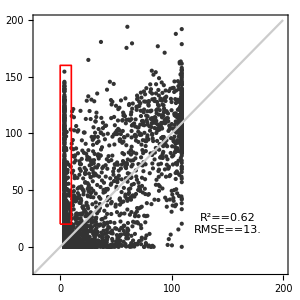
-Graphics-PSI global epistasisPSI measurement

```mathematica
figgescatter=Labeled[
Show[
ListPlot[
Transpose@{yhat,responseSmn1[[seqlistSmn1]]},
BaseStyle->{FontSize->fontsize},
PlotStyle->{{GrayLevel[.2],PointSize[.01]}},
PlotRange->{{-20,200},{-20,200}},
AspectRatio->1,
Axes->False,
Frame->True,
FrameStyle->fstyle,
FrameTicks->{{Range[0,200,50],False},{Range[0,200,50],False}},
FrameLabel->None,
PlotLabel->Style["",Black,FontSize->16]],Plot[x,{x,-100,200},PlotStyle->GrayLevel[.8]],
Graphics[
Inset[
Column[
{Style[Style[Subscript[Superscript[R,2],""],Italic]==Round[r2[yhat,responseSmn1[[seqlistSmn1]]],.01],GrayLevel[.2],FontSize->16],
 Style[Style[Subscript[RMSE,""],Italic]==Round[Sqrt@mse[yhat,responseSmn1[[seqlistSmn1]]],.1],GrayLevel[.2],FontSize->16]},
Alignment->Left],{150,20}]],
Graphics[{EdgeForm[{Thickness[.004],Red}],Transparent,box}],
ImageSize->300],
Style[#,FontFamily->"Helvetica",FontSize->fontsize,GrayLevel[.2]]&/@{"PSI global epistasis","PSI measurement"},{Bottom,Left},RotateLabel->True]
```

```mathematica
outliersAll=seqlistSmn1[[Flatten@Position[RegionMember[box,Transpose[{yhat,responseSmn1[[seqlistSmn1]]}]],True]]];
%//Length
```

1500

```mathematica
outliersSmn1=seqlistSmn1[[Flatten@Position[Boole[#<0.5&/@phi]*Boole[#>50&/@y],1]]];
%//Length
```

244

```mathematica
outliersSub=Join[outliersSmn1,RandomSample[Complement[outliersAll,outliersSmn1],200]];
```

```mathematica
outliersSub >> "GE/outliers.m"
```

```mathematica
outliersLOO=Table[{},Length[outliersSub]];
```

```mathematica
(*Do[{Print[i],outliersLOO[[i]]=VCLS[Complement[seqlistSmn1,{outliersSub[[i]]}],responseSmn1[[Complement[seqlistSmn1,{outliersSub[[i]]}]]],MapPartialVal[seqlistSmn1,variance,alpha^l][[Complement[seqlistSmn1,{outliersSub[[i]]}]]]]},{i,Length[outliersSub]}]*)
```

```mathematica
outliersSub = Import["GE/outliers.m"];
outliersLOO =Join[Get[ "out/Smn1_VC_outliersLOO.m"],Get["out/outliers2subset1LOO.m"]];
```

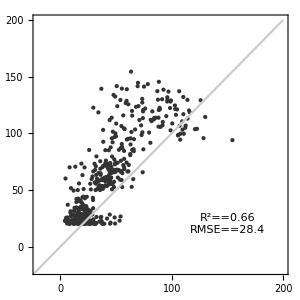
-Graphics-PSI VCPSI measurement

```mathematica
figgeoutliers=Labeled[
Show[
ListPlot[
Transpose@{outliersLOO,responseSmn1[[outliersSub]]},
BaseStyle->{FontSize->fontsize},
PlotStyle->{{GrayLevel[.2],PointSize[.01]}},
PlotRange->{{-20,200},{-20,200}},
AspectRatio->1,
Axes->False,
Frame->True,
FrameStyle->fstyle,
FrameTicks->{{Range[0,200,50],False},{Range[0,200,50],False}},
FrameLabel->None,
PlotLabel->Style["",Black,FontSize->16]],Plot[x,{x,-100,200},PlotStyle->GrayLevel[.8]],
Graphics[
Inset[
Column[
{Style[Style[Subscript[Superscript[R,2],""],Italic]==Round[r2[outliersLOO,responseSmn1[[outliersSub]]],.01],GrayLevel[.2],FontSize->16],
 Style[Style[Subscript[RMSE,""],Italic]==Round[Sqrt@mse[outliersLOO,responseSmn1[[outliersSub]]],.1],GrayLevel[.2],FontSize->16]},
Alignment->Left],{150,20}]],
ImageSize->300],
Style[#,FontFamily->"Helvetica",FontSize->fontsize,GrayLevel[.2]]&/@{"PSI VC","PSI measurement"},{Bottom,Left},RotateLabel->True]
```

```mathematica
Grid[{labelfigs[{figgescatter,figgeoutliers}]}];
```

```mathematica
Export[FileNameJoin[{figpath,"5ss_ge_outliers.pdf"}],%];
```

```mathematica
FileNameJoin[{figpath,"5ss_ge_outliers.pdf"}]
```

/Users/keitokiddo/VC/figures/5ss_ge_outliers.pdf

### GE outliers validation

```mathematica
seqsGEoutliers=Flatten@Import[StringJoin[wd,"low_throughput_results/manualset1seqs.tsv"]];
```

```mathematica
dataGEoutliers=Import[StringJoin[wd,"low_throughput_results/012219_Validation_quant_processed.xlsx"],"XLSX"][[1]];
```

```mathematica
dataGEoutliers[[2;;,3]]=StringReplace[#,"T"->"U"]&/@dataGEoutliers[[2;;,3]];
dataGEoutliers[[2;;,3]]=StringReplace[#," "->""]&/@dataGEoutliers[[2;;,3]];
```

```mathematica
dataGEoutliers=Join[dataGEoutliers[[{1}]],dataGEoutliers[[36;;]]];
```

```mathematica
dataGEoutliers=dataGEoutliers[[All,{3,8,4}]];
```

```mathematica
dataGEoutliers=Pick[dataGEoutliers[[2;;]],MemberQ[sequences9AA[[outliersAll]],#]&/@dataGEoutliers[[2;;,1]]];
```

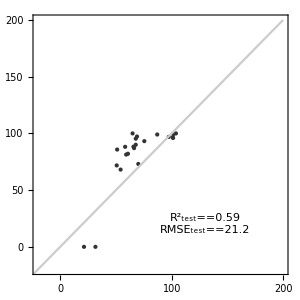
-Graphics-PSI libraryPSI manual

```mathematica
Labeled[ScatterPlot[responseSmn1[[seq2pos9AA/@dataGEoutliers[[All,1]]]],dataGEoutliers[[All,2]],""],Style[#,FontFamily->"Helvetica",FontSize->16]&/@{"PSI library","PSI manual"},{Bottom,Left},RotateLabel->True]
```

```mathematica
Export[FileNameJoin[{figpath,"5ss_ge_outliers_validation.pdf"}],%];
```

## Manual validation of unsampled Smn1 sequences

```mathematica
SetDirectory[wd];
```

```mathematica
figgel = Import["low_throughput_results/Gel_images.002.jpeg"];
figgel = ImageCrop[figgel];
(*figgel = Framed[figgel,BaseStyle->Transparent,ImageMargins->{{5,0},{0,0}}];*)
```

```mathematica
figgel
```

-Graphics-

```mathematica
dataLT=Import["low_throughput_results/5ss_low_throughput_results.csv","CSV"];
```

```mathematica
U2T[seq_]:=StringJoin[Characters[seq]/.{"U"->"T"}]
T2U[seq_]:=StringJoin[Characters[seq]/.{"T"->"U"}]
```

```mathematica
seqlistLT=seq2pos9AA/@T2U/@dataLT[[2;;,1]];
```

#### Calculate posterior variances

```mathematica
VarLT=Table[0,Length[seqlistLT]];
Do[VarLT[[i]]=GPVar[lambdas,seqlistSmn1,Smn1Std^2,sequences[[seqlistLT]][[i]]],{i,Length[seqlistLT]}];//AbsoluteTiming
```

{2735.77,Null}

#### Measured PSI vs. prediction

```mathematica
plotdat=Table[{Around[truncate@dataLT[[i+1,2]],Sqrt[VarLT[[i]]]],Around[truncate@dataLT[[i+1,4]],dataLT[[i+1,5]]+.001]},{i,Length[dataLT]-1}];
```

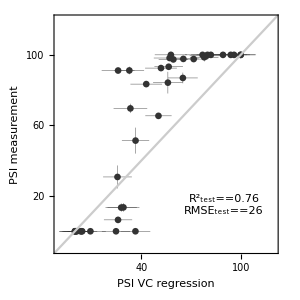

```mathematica
figlowthroughputvsVC=Show[ListPlot[plotdat,BaseStyle->{FontSize->fontsize-2},PlotStyle->{{GrayLevel[0.2],PointSize[0.016],Thickness[.001]}},PlotRange->{{-10,120},{-10,120}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"PSI VC regression","PSI measurement"},FrameTicks->{{Range[-20,200,20],False},{Range[-20,200,20],False}},FrameStyle->fstyle],Plot[x,{x,-100,200},PlotStyle->GrayLevel[0.8]],Graphics[Inset[Column[{Style[Style[Subscript[Superscript[R,2],"test"],Italic]==Round[r2[plotdat[[All,1,1]],plotdat[[All,2,1]]],.01],FontSize->14], Style[Style[Subscript[RMSE,"test"],Italic]==Round[Sqrt[mse[plotdat[[All,1,1]],plotdat[[All,2,1]]]],1],FontSize->14]},Alignment->Left],{90,15}]],ImageSize->300]
```

```mathematica
plotdat=labelfigs[{Show[figgel,ImageSize->{Automatic,270}],figlowthroughputvsVC}];
```

```mathematica
Grid[{plotdat},Spacings->{4},Alignment->Top]
```

-Graphics-A | -Graphics-B

```mathematica
Export[FileNameJoin[{figpath,"fig6_5ss_manual_gel_r2.pdf"}],%];
```

### New supplemental figure library scatter + low throughput scatter

#### Measured PSI vs. prediction

```mathematica
pdsAll={pdsVC,pds1way,pdsGE,pds2wayEN,pds3wayEN};
dataLT=Import["low_throughput_results/5ss_low_throughput_results.csv","CSV"];
```

```mathematica
i=-3;
j=1;
```

```mathematica
ts=Complement[seqlistSmn1,trs[[i,j]]];
```

```mathematica
plotdat=Table[pdsAll[[k]][[i,j]],{k,Length[pdsAll]}];
```

```mathematica
panelA=Show[
ListPlot[
Transpose@{plotdat[[1]][[ts]],responseSmn1[[ts]]},
BaseStyle->{FontSize->fontsize},
PlotStyle->{{GrayLevel[.2],PointSize[.01]}},
PlotRange->{{-20,200},{-20,200}},
AspectRatio->1,
Frame->True,
FrameTicks->{{Range[0,200,50],False},{Range[0,200,50],False}},
FrameStyle->fstyle,
FrameLabel->{StringJoin["PSI ", modelnames[[1]]],"PSI high-throughput"},
ImageSize->400],
Plot[x,{x,-100,200},PlotStyle->GrayLevel[.8]],
Graphics[Inset[Column[{Style[Style[Subscript[Superscript[R,2],"test"],Italic]==Round[r2[plotdat[[1]][[ts]],responseSmn1[[ts]]],.01],GrayLevel[.2],FontSize->16], Style[Style[Subscript[RMSE,"test"],Italic]==Round[Sqrt@mse[plotdat[[1]][[ts]],responseSmn1[[ts]]],.1],GrayLevel[.2],FontSize->16]},Alignment->Left],{150,20}]]];
```

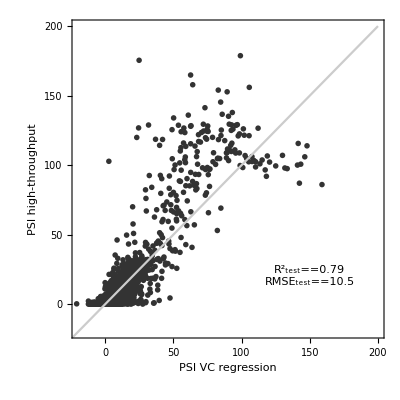
-Graphics-A

```mathematica
panelA=Labeled[
panelA,
Style["A",Bold,FontFamily->"Helvetica",FontSize->fontsize],{{Top,Left}}
]
```

```mathematica
plotdat=Table[{Around[dataLT[[i+1,2]],Sqrt[VarLT[[i]]]],Around[dataLT[[i+1,4]],dataLT[[i+1,5]]+.001]},{i,Length[dataLT]-1}];
```

```mathematica
panelB=Show[
ListPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
PlotStyle->{{GrayLevel[.2],PointSize[.01]}},
PlotRange->{{-20,200},{-20,200}},
AspectRatio->1,
Frame->True,
FrameTicks->{{Range[0,200,50],False},{Range[0,200,50],False}},
FrameStyle->fstyle,
FrameLabel->{StringJoin["PSI ", modelnames[[1]]],"PSI low-throughput"},
ImageSize->400],
Plot[x,{x,-100,200},PlotStyle->GrayLevel[.8]],
Graphics[Inset[Column[{Style[Style[Subscript[Superscript[R,2],"test"],Italic]==NumberForm[Round[r2[plotdat[[All,1,1]],plotdat[[All,2,1]]],.01],{2,2}],GrayLevel[.2],FontSize->16], Style[Style[Subscript[RMSE,"test"],Italic]==Round[Sqrt@mse[plotdat[[All,1,1]],plotdat[[All,2,1]]],.1],GrayLevel[.2],FontSize->16]},Alignment->Left],{150,20}]]];
```

```mathematica
panelB=Labeled[
panelB,
Style["B",Bold,FontFamily->"Helvetica",FontSize->fontsize],{{Top,Left}}
];
```

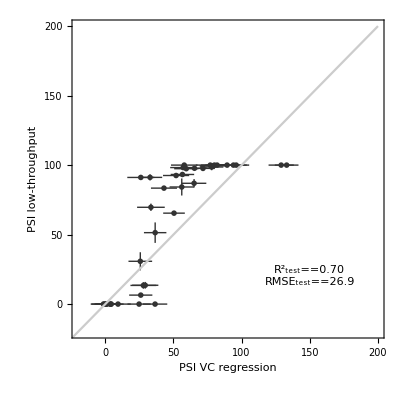
-Graphics-A | -Graphics-B

```mathematica
Grid[{{panelA,panelB}}, Spacings->{3, 10}]
```

```mathematica
Grid[{{panelA,panelB}}, Spacings->{3, 10}]
```

-Graphics-A | -Graphics-B

```mathematica
Export[StringJoin[figpath,"/prediction_ht_lt_scatter.pdf"],%];
```

```mathematica
figpath
```

/Users/keitokiddo/VC/figures